```mathematica
experiments={
"EYrainbow_glucose",
"EYrainbow_glucose_largerBF",
"EYrainbow_rapamycin_1stTry",
"EYrainbow_rapamycin_CheckBistability",
"EYrainbow_1nmpp1_1st",
"EYrainbow_leucine_large",
"EYrainbowWhi5Up_betaEstrodiol"
};
data = Import[FileNameJoin[{NotebookDirectory[],"fitCellSizeWithOrganelle_normal.csv"}],"Data","HeaderLines"->1];
epsilon = 10^(-18);
filled = data/.{0.->epsilon};
washed = Select[data,Function[x,NoneTrue[x,#==0&]]];
```

```mathematica
(* Check data *)
Position[filled,0.]
Position[washed,0.]
```

{}

{}

```mathematica
Length[filled]
Length[washed]
```

9744

6214

```mathematica
fitCellSizeFromOrganelles[dataset_]:=Module[
{expr,a,b,c,alpha,mean,n,nlm,params,fittedFunc,fitted,fittedMin,fittedMax,dataMin,dataMax},
expr = Sum[a[i]n[i]mean[i]^alpha[i],{i,1,6}]+Sum[n[i]mean[i]^alpha[i]b[i,j]n[j]mean[j]^alpha[j],{i,1,5},{j,i+1,6}]+c;
nlm = NonlinearModelFit[
dataset[[All,2;;]],expr,
Join[
Table[a[i],{i,1,6}],
Flatten[Table[b[i,j],{i,1,5},{j,i+1,6}]],
{c},
Table[alpha[i],{i,1,6}]
],
Join[
Table[mean[i],{i,1,6}],
Table[n[i],{i,1,6}]
],
MaxIterations->∞
];
params=nlm["BestFitParameters"];
Print["a[i]: ",Table[a[i],{i,1,6}]/.params];
Print["b[i,j]: ",Table[b[i,j],{i,1,6},{j,1,6}]/.params//MatrixForm];
Print["c: ", c/.params];
Print["alpha[i]: ",Table[alpha[i],{i,1,6}]/.params];
Print["Adjusted R Square: ", nlm["AdjustedRSquared"]];
Print["p-values for parameter z-statistics: ", nlm["ParameterPValues"]];
Print["t-statistics for parameter estimates: ", nlm["ParameterTStatistics"]];
fittedFunc = Function[
vec,
expr/.params
/.Table[n[i]->vec[[i]],{i,1,6}]
/.Table[mean[i]->vec[[i+6]],{i,1,6}]
];
fitted = Map[fittedFunc,dataset[[All,2;;-2]]];
fittedMin = Min[fitted];
fittedMax = Max[fitted];
dataMin = Min[dataset[[All,-1]]];
dataMax = Max[dataset[[All,-1]]];
Print[Show[
ListPlot[
Transpose[{dataset[[All,-1]],fitted}],
PlotTheme->"Scientific"
],
Plot[x,{x,0,dataMax}]
]];
Print[""]
]
```

All Experiments, Null Organelles filled with 0:

a[i]: {2.64903,0.319275,0.0628447,0.146391,2.59413,-2.32901}

b[i,j]: (b$17844[1,1] | -0.00162656 | 0.000492928 | -0.030026 | 0.0494521 | 0.103361
b$17844[2,1] | b$17844[2,2] | 1.69267×10^-6 | -0.000879273 | -0.00193606 | -0.00149458
b$17844[3,1] | b$17844[3,2] | b$17844[3,3] | -0.000079656 | -0.0000426997 | -0.00078432
b$17844[4,1] | b$17844[4,2] | b$17844[4,3] | b$17844[4,4] | 0.0525309 | -0.0280443
b$17844[5,1] | b$17844[5,2] | b$17844[5,3] | b$17844[5,4] | b$17844[5,5] | 0.0559782
b$17844[6,1] | b$17844[6,2] | b$17844[6,3] | b$17844[6,4] | b$17844[6,5] | b$17844[6,6])

c: 45.5318

alpha[i]: {0.895575,1.33969,1.98626,-0.73078,0.686293,1.2587}

Adjusted R Square: 0.953567

p-values for parameter z-statistics: {2.36303×10^-10,1.35735×10^-16,0.000182802,0.100506,3.73562×10^-50,7.36639×10^-8,0.000044572,0.057952,0.00141744,0.0405456,0.000511704,0.56153,0.0000917503,0.0000164045,0.0821526,0.116694,0.626644,0.0158957,1.04143×10^-24,0.00305119,0.0123806,4.14221×10^-91,9.20425×10^-124,0.,6.42577×10^-159,4.33698×10^-58,0.,3.88369×10^-24}

t-statistics for parameter estimates: {6.34239,8.28321,3.74311,1.64256,14.9774,-5.38615,-4.08426,1.89628,-3.192,2.04842,3.47572,0.58059,-3.91307,-4.3111,-1.73851,-1.56894,-0.486472,-2.41172,10.2905,-2.96328,2.50157,20.4583,24.0061,53.2415,27.3673,-16.1749,88.0526,10.1616}

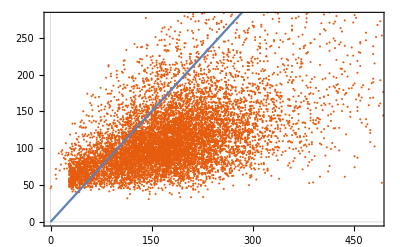

```mathematica
Print["All Experiments, Null Organelles filled with 0:"];
fitCellSizeFromOrganelles[filled];
```

All Experiments, Null Organelles Excluded:

a[i]: {3.47326,0.792393,0.104546,0.562079,0.0179463,-0.271061}

b[i,j]: (b$18326[1,1] | -0.00344124 | 0.00166971 | -0.0437249 | -0.0895908 | 0.0518534
b$18326[2,1] | b$18326[2,2] | -0.0000710892 | -0.00129985 | -0.00407788 | 0.00118305
b$18326[3,1] | b$18326[3,2] | b$18326[3,3] | 0.000231988 | 0.00136929 | -0.00131995
b$18326[4,1] | b$18326[4,2] | b$18326[4,3] | b$18326[4,4] | 0.0482466 | -0.0140692
b$18326[5,1] | b$18326[5,2] | b$18326[5,3] | b$18326[5,4] | b$18326[5,5] | 0.0436904
b$18326[6,1] | b$18326[6,2] | b$18326[6,3] | b$18326[6,4] | b$18326[6,5] | b$18326[6,6])

c: 55.6453

alpha[i]: {0.931525,1.17684,1.82988,-0.398609,0.790704,-0.43754}

Adjusted R Square: 0.965648

p-values for parameter z-statistics: {3.76287×10^-12,4.70766×10^-23,0.00253352,0.00104195,0.940107,0.0284828,0.0000322013,0.0562048,0.00455619,0.000310935,0.0000200341,0.0304665,0.0610444,1.67549×10^-6,0.0217549,0.279996,0.0430571,0.0169287,3.23385×10^-9,0.0000999296,2.98052×10^-12,5.01915×10^-55,1.47512×10^-81,0.,8.18483×10^-89,1.20591×10^-12,0.,9.16478×10^-11}

t-statistics for parameter estimates: {6.95966,9.92729,3.02054,3.28051,0.0751381,-2.19108,-4.16039,1.9098,-2.83788,-3.60806,4.26782,-2.16447,-1.87352,-4.79371,2.2952,1.08042,2.02357,-2.3889,5.9279,-3.8933,6.99268,15.7798,19.4152,54.8,20.3078,-7.1195,85.7453,-6.4914}

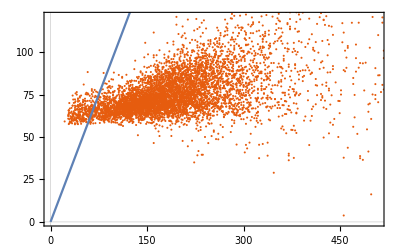

```mathematica
Print["All Experiments, Null Organelles Excluded:"];
fitCellSizeFromOrganelles[washed];
```

EYrainbow_glucose, Null Organelles filled with 0:

a[i]: {2.25529,0.0415654,0.393512,-5.22931,6.00122,0.970455}

b[i,j]: (b$18808[1,1] | -0.00396857 | -0.014997 | -0.245722 | 0.131322 | 0.922111
b$18808[2,1] | b$18808[2,2] | 0.0000406576 | 0.000773604 | 0.000685802 | -0.00202324
b$18808[3,1] | b$18808[3,2] | b$18808[3,3] | 0.016604 | -0.00552205 | 0.0132314
b$18808[4,1] | b$18808[4,2] | b$18808[4,3] | b$18808[4,4] | 0.140637 | -0.815431
b$18808[5,1] | b$18808[5,2] | b$18808[5,3] | b$18808[5,4] | b$18808[5,5] | -0.191087
b$18808[6,1] | b$18808[6,2] | b$18808[6,3] | b$18808[6,4] | b$18808[6,5] | b$18808[6,6])

c: -7.36138

alpha[i]: {0.915646,1.63196,1.65024,0.800632,0.690578,0.115422}

Adjusted R Square: 0.961505

p-values for parameter z-statistics: {0.525251,0.170518,0.384643,0.0260467,1.65172×10^-7,0.609262,0.184777,0.508321,0.495629,0.432715,0.00248992,0.558943,0.388332,0.318838,0.276338,0.555074,0.403348,0.52787,0.265221,0.00324127,0.0905573,0.559554,1.21134×10^-18,1.58984×10^-26,1.44999×10^-6,4.62819×10^-7,3.85538×10^-54,0.50831}

t-statistics for parameter estimates: {0.635626,1.3721,0.869977,-2.23077,5.29418,0.511383,-1.32764,-0.661831,-0.681778,0.785056,3.03675,0.584722,0.863241,0.997635,-1.08953,0.590488,-0.836218,0.631611,1.11513,-2.95518,-1.69506,-0.583814,9.09533,11.1608,4.86454,5.09427,17.0955,0.661848}

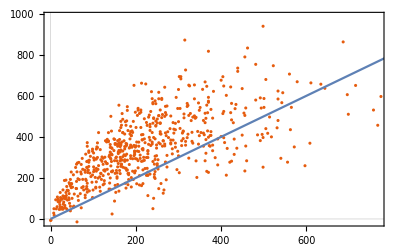

EYrainbow_glucose_largerBF, Null Organelles filled with 0:

a[i]: {-6.08493,0.0232464,1.03449×10^-10,7.13259,11.0575,-0.43553}

b[i,j]: (b$18946[1,1] | 0.000026469 | -5.48978×10^-11 | 0.451918 | 0.317352 | 0.192775
b$18946[2,1] | b$18946[2,2] | 6.10422×10^-15 | 0.000491931 | -0.000522362 | 0.0000374099
b$18946[3,1] | b$18946[3,2] | b$18946[3,3] | 9.41269×10^-12 | 2.92256×10^-11 | -2.53825×10^-11
b$18946[4,1] | b$18946[4,2] | b$18946[4,3] | b$18946[4,4] | -0.755543 | 0.424949
b$18946[5,1] | b$18946[5,2] | b$18946[5,3] | b$18946[5,4] | b$18946[5,5] | -0.0517878
b$18946[6,1] | b$18946[6,2] | b$18946[6,3] | b$18946[6,4] | b$18946[6,5] | b$18946[6,6])

c: -65.8228

alpha[i]: {0.904679,2.15835,6.78344,1.65885,0.744653,0.200769}

Adjusted R Square: 0.967636

p-values for parameter z-statistics: {0.,5.25703×10^-8,0.524438,0.,0.,0.,0.946472,1.11747×10^-11,0.,2.16431×10^-49,4.23696×10^-32,0.0982894,0.0967173,8.21046×10^-9,0.801009,0.0444237,1.11815×10^-29,1.93718×10^-6,1.73275×10^-274,2.30032×10^-200,5.62853×10^-10,0.,0.,0.,0.,0.,0.,1.8475×10^-85}

t-statistics for parameter estimates: {-11851.8,5.4928,0.636789,11461.6,10646.2,-598.677,0.0671586,-6.88768,130.061,15.8017,12.3068,1.65506,1.66286,-5.82381,0.252122,2.01312,11.7667,-4.79387,-54.0326,40.7231,-6.27465,-1.06438×10^6,792.475,4084.45,19066.6,1748.1,79.8364,22.0879}

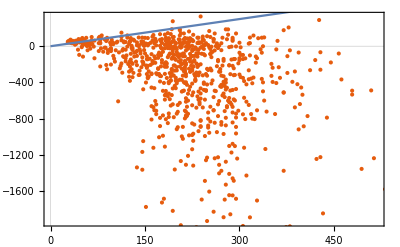

EYrainbow_rapamycin_1stTry, Null Organelles filled with 0:

a[i]: {8.29789,0.0769519,0.057453,-2.43186,-0.171198,0.973342}

b[i,j]: (b$19100[1,1] | -0.00478623 | 0.000648476 | -0.89196 | -0.007849 | -0.108691
b$19100[2,1] | b$19100[2,2] | 2.57139×10^-6 | 0.000181402 | 0.0000866572 | -0.00170415
b$19100[3,1] | b$19100[3,2] | b$19100[3,3] | 0.00122592 | -0.0000174606 | -0.000326064
b$19100[4,1] | b$19100[4,2] | b$19100[4,3] | b$19100[4,4] | 0.00371506 | -0.0365451
b$19100[5,1] | b$19100[5,2] | b$19100[5,3] | b$19100[5,4] | b$19100[5,5] | 0.00736798
b$19100[6,1] | b$19100[6,2] | b$19100[6,3] | b$19100[6,4] | b$19100[6,5] | b$19100[6,6])

c: 86.542

alpha[i]: {0.458319,1.80915,2.08631,2.81677,1.88768,0.074722}

Adjusted R Square: 0.94345

p-values for parameter z-statistics: {5.12501×10^-9,0.271101,0.141832,0.234516,0.238693,0.0422478,0.276795,0.572469,0.0631035,0.361516,0.251132,0.61899,0.961456,0.357301,0.266706,0.474443,0.492393,0.310538,0.683681,0.795315,0.224841,7.79389×10^-91,0.0000185388,1.35369×10^-16,1.26257×10^-25,0.0000228507,2.55641×10^-10,0.601904}

t-statistics for parameter estimates: {5.88438,1.10102,1.46993,-1.18938,-1.17882,2.03315,-1.08802,0.564568,-1.86012,-0.912815,-1.14814,0.497407,0.0483362,0.920861,-1.11118,0.715484,-0.68671,-1.01451,0.40754,-0.259471,1.21436,21.9856,4.29841,8.38484,10.6997,4.25114,6.37574,0.521797}

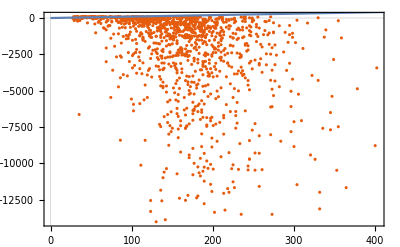

EYrainbow_rapamycin_CheckBistability, Null Organelles filled with 0:

a[i]: {-3.88743,0.0463887,0.257874,3.73558,-1.16468,-1.10043}

b[i,j]: (b$19238[1,1] | -0.000654589 | 0.00146986 | -0.168344 | 0.287393 | -0.211467
b$19238[2,1] | b$19238[2,2] | 1.32891×10^-6 | -0.000209559 | -0.000648105 | 0.0000459076
b$19238[3,1] | b$19238[3,2] | b$19238[3,3] | 0.00103063 | -0.0011708 | -0.00220837
b$19238[4,1] | b$19238[4,2] | b$19238[4,3] | b$19238[4,4] | -0.216004 | 0.284433
b$19238[5,1] | b$19238[5,2] | b$19238[5,3] | b$19238[5,4] | b$19238[5,5] | 0.0690958
b$19238[6,1] | b$19238[6,2] | b$19238[6,3] | b$19238[6,4] | b$19238[6,5] | b$19238[6,6])

c: 70.7118

alpha[i]: {1.26687,1.98602,1.82981,-0.111692,0.926681,0.560651}

Adjusted R Square: 0.963039

p-values for parameter z-statistics: {9.28197×10^-11,0.102387,0.000170661,0.0000210132,0.0000161974,0.0352461,0.103596,0.110976,0.000764313,1.96326×10^-13,6.57644×10^-8,0.690364,0.397826,0.120715,0.817759,0.244582,0.037227,0.0405829,0.0000183196,0.0000109561,0.0000190092,6.82205×10^-76,8.79766×10^-70,3.29576×10^-37,3.75683×10^-134,0.356956,2.75235×10^-308,2.63851×10^-10}

t-statistics for parameter estimates: {-6.50057,1.63387,3.76346,4.26036,-4.31852,-2.10644,-1.62814,1.59428,-3.36873,7.38381,-5.41546,0.398398,-0.845627,-1.5522,0.230448,1.16383,-2.08416,-2.04862,-4.2911,4.40456,4.28284,18.9505,18.1101,12.9144,25.9012,-0.921316,42.1978,6.33943}

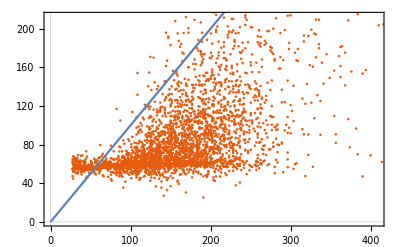

EYrainbow_1nmpp1_1st, Null Organelles filled with 0:

a[i]: {2.73439,0.213713,0.154328,-2.74601,5.23132,-4.66461}

b[i,j]: (b$19376[1,1] | -0.0026659 | -0.00144172 | -0.431363 | 0.235087 | -0.494927
b$19376[2,1] | b$19376[2,2] | 0.0000201859 | -0.02989 | -0.0048514 | -0.00179706
b$19376[3,1] | b$19376[3,2] | b$19376[3,3] | 0.0100175 | -0.00222036 | 0.00464416
b$19376[4,1] | b$19376[4,2] | b$19376[4,3] | b$19376[4,4] | -0.285396 | 1.13894
b$19376[5,1] | b$19376[5,2] | b$19376[5,3] | b$19376[5,4] | b$19376[5,5] | 0.0680297
b$19376[6,1] | b$19376[6,2] | b$19376[6,3] | b$19376[6,4] | b$19376[6,5] | b$19376[6,6])

c: 7.89439

alpha[i]: {0.918863,1.63278,1.82884,2.71568,0.660611,1.0918}

Adjusted R Square: 0.962047

p-values for parameter z-statistics: {0.110225,0.0593623,0.0775009,0.505956,1.12179×10^-19,0.00653699,0.203375,0.303991,0.415144,0.0124226,0.00850862,0.359756,0.173253,0.110285,0.285362,0.188547,0.0877148,0.220085,0.33663,0.0267669,0.509127,0.26919,8.71351×10^-16,2.05373×10^-34,1.37081×10^-31,6.79409×10^-11,9.36774×10^-141,0.0000936003}

t-statistics for parameter estimates: {1.59806,1.88683,1.7665,-0.665296,9.19511,-2.7231,-1.27251,-1.02824,-0.815085,2.50272,-2.63443,0.916091,-1.36243,-1.59779,-1.06871,1.31545,-1.70862,1.22678,-0.961132,2.21693,0.660345,1.10531,8.12642,12.5252,11.9482,6.56949,27.9803,3.91648}

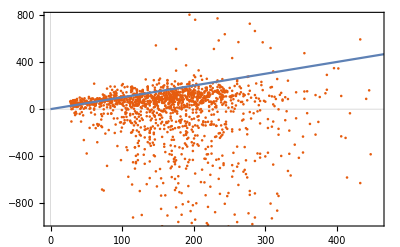

EYrainbow_leucine_large, Null Organelles filled with 0:

a[i]: {0.746557,0.020011,0.963743,0.32088,-1.23276,0.195301}

b[i,j]: (b$19514[1,1] | 0.0000257428 | 0.00158772 | 0.0180724 | -0.0326575 | -0.0221794
b$19514[2,1] | b$19514[2,2] | 1.87371×10^-6 | 0.0000370207 | -0.000800724 | 0.000282576
b$19514[3,1] | b$19514[3,2] | b$19514[3,3] | -0.00440537 | 0.00918238 | -0.00416238
b$19514[4,1] | b$19514[4,2] | b$19514[4,3] | b$19514[4,4] | -0.0125332 | 0.0225078
b$19514[5,1] | b$19514[5,2] | b$19514[5,3] | b$19514[5,4] | b$19514[5,5] | 0.0207728
b$19514[6,1] | b$19514[6,2] | b$19514[6,3] | b$19514[6,4] | b$19514[6,5] | b$19514[6,6])

c: 22.1809

alpha[i]: {1.42703,1.88932,1.42079,-1.07062,0.712871,-0.376682}

Adjusted R Square: 0.980123

p-values for parameter z-statistics: {0.23263,0.346508,0.00483476,0.0964298,0.0130564,0.397661,0.892151,0.625939,0.360232,0.380176,0.292725,0.890888,0.739384,0.409818,0.429563,0.0312213,0.0888892,0.0576414,0.484819,0.0230917,0.00662439,0.0000336982,4.98552×10^-6,2.08127×10^-13,9.18853×10^-49,0.,2.98535×10^-35,0.0309894}

t-statistics for parameter estimates: {1.1941,0.941686,2.82211,1.66347,-2.48524,0.846052,0.135607,0.487553,0.915209,-0.877835,-1.05254,0.137204,0.332732,-0.824449,0.790158,-2.1563,1.70241,-1.8999,-0.698749,2.27429,2.71901,4.15972,4.58233,7.41228,15.2304,-151.527,12.7205,-2.15927}

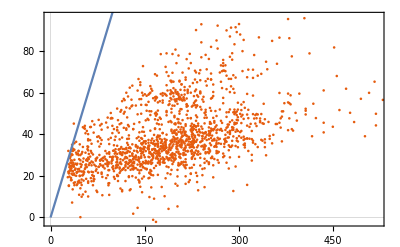

EYrainbowWhi5Up_betaEstrodiol, Null Organelles filled with 0:

a[i]: {2.0793,0.52773,0.0446242,1.649,5.41932,-3.51815}

b[i,j]: (b$19652[1,1] | -0.00301458 | -0.00198516 | -0.0488296 | 0.552687 | -0.265232
b$19652[2,1] | b$19652[2,2] | 0.0000109739 | 0.000964784 | -0.00997489 | 0.00100441
b$19652[3,1] | b$19652[3,2] | b$19652[3,3] | 0.000530961 | -0.00140965 | 0.00258127
b$19652[4,1] | b$19652[4,2] | b$19652[4,3] | b$19652[4,4] | -0.054373 | -0.154225
b$19652[5,1] | b$19652[5,2] | b$19652[5,3] | b$19652[5,4] | b$19652[5,5] | 0.114994
b$19652[6,1] | b$19652[6,2] | b$19652[6,3] | b$19652[6,4] | b$19652[6,5] | b$19652[6,6])

c: -6.16198

alpha[i]: {1.1693,1.28197,2.10701,-0.931655,0.719818,1.1015}

Adjusted R Square: 0.975453

p-values for parameter z-statistics: {0.23304,0.00128631,0.361611,0.0233616,0.00112365,0.237336,0.03796,0.415906,0.174291,0.0000120084,0.107049,0.454678,0.208678,0.0045007,0.759962,0.444468,0.374011,0.412249,0.15758,0.0229573,0.560731,0.71841,1.42168×10^-43,1.32915×10^-70,8.48544×10^-13,0.0000535896,3.50052×10^-137,4.48283×10^-7}

t-statistics for parameter estimates: {1.19372,3.23375,0.91297,2.27307,3.27283,-1.18281,-2.07972,-0.814087,-1.3601,4.4131,-1.61393,0.748107,1.25851,-2.85113,0.305665,0.765157,-0.889625,0.820493,-1.41496,-2.27979,0.582068,-0.360748,14.9845,20.2807,7.30552,-4.06764,32.6757,5.10134}

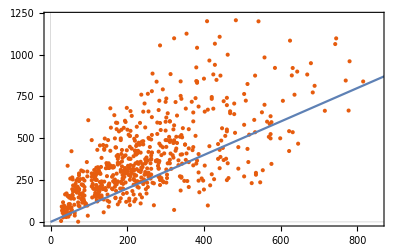

```mathematica
Do[
Print[experiments[[i]],", Null Organelles filled with 0:"];
fitCellSizeFromOrganelles[Select[filled,#[[1]]==experiments[[i]]&]];,
{i,1,Length[experiments]}
];
```

EYrainbow_glucose, Null Organelles Excluded:

a[i]: {1.93135,0.159665,0.351302,-1.69587,4.75228,5.22071}

b[i,j]: (b$20119[1,1] | -0.0130452 | -0.0239446 | -0.233265 | 0.137003 | 1.36801
b$20119[2,1] | b$20119[2,2] | 0.000112627 | 0.00217108 | 0.00253537 | -0.00780164
b$20119[3,1] | b$20119[3,2] | b$20119[3,3] | 0.0262174 | -0.00267348 | 0.0242738
b$20119[4,1] | b$20119[4,2] | b$20119[4,3] | b$20119[4,4] | 0.0846012 | -1.35488
b$20119[5,1] | b$20119[5,2] | b$20119[5,3] | b$20119[5,4] | b$20119[5,5] | -0.369588
b$20119[6,1] | b$20119[6,2] | b$20119[6,3] | b$20119[6,4] | b$20119[6,5] | b$20119[6,6])

c: -10.7139

alpha[i]: {0.836263,1.40684,1.60043,0.752815,0.695855,0.235989}

Adjusted R Square: 0.969315

p-values for parameter z-statistics: {0.729843,0.137163,0.504929,0.681077,0.0114856,0.154369,0.150372,0.645717,0.617595,0.526987,0.00623393,0.690053,0.455801,0.311859,0.251025,0.680878,0.629241,0.675404,0.63067,0.00444472,0.0606431,0.692885,2.38531×10^-14,4.51661×10^-22,0.00176363,0.000121636,6.62415×10^-23,0.231873}

t-statistics for parameter estimates: {0.345616,1.48992,0.667458,-0.411344,2.54125,1.42742,-1.44144,-0.460127,-0.499717,0.633258,2.75222,0.39912,0.746626,1.01282,-1.14981,0.411616,-0.48323,0.419101,0.481215,-2.86371,-1.88229,-0.395276,7.96939,10.3626,3.15215,3.88742,10.6023,1.19767}

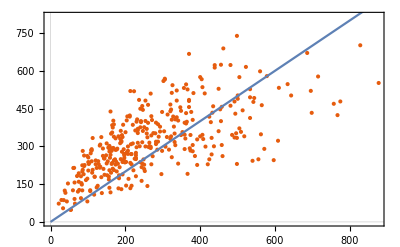

EYrainbow_glucose_largerBF, Null Organelles Excluded:

a[i]: {-15.667,1.15408,8.97129×10^-11,9.35004,9.11458,0.630652}

b[i,j]: (b$20256[1,1] | -0.0466238 | -9.49998×10^-11 | 0.877159 | 1.05713 | -0.15433
b$20256[2,1] | b$20256[2,2] | -6.48053×10^-13 | 0.0107775 | -0.0164349 | 0.00391832
b$20256[3,1] | b$20256[3,2] | b$20256[3,3] | -1.81347×10^-11 | 2.84314×10^-11 | -1.53034×10^-12
b$20256[4,1] | b$20256[4,2] | b$20256[4,3] | b$20256[4,4] | -0.633487 | 0.0557303
b$20256[5,1] | b$20256[5,2] | b$20256[5,3] | b$20256[5,4] | b$20256[5,5] | -0.0218523
b$20256[6,1] | b$20256[6,2] | b$20256[6,3] | b$20256[6,4] | b$20256[6,5] | b$20256[6,6])

c: -63.7285

alpha[i]: {0.826969,1.15186,6.73529,1.28274,0.741676,-0.528911}

Adjusted R Square: 0.974121

p-values for parameter z-statistics: {0.,0.0883728,0.751985,0.,1.01741×10^-36,0.214965,0.274788,0.806158,0.0382295,8.06022×10^-9,0.259568,0.79194,0.606887,0.0862753,0.419061,0.794927,0.806401,0.80487,1.09585×10^-12,0.249909,0.154037,0.,6.89923×10^-18,1.25895×10^-11,5.04408×10^-11,1.13202×10^-8,1.90021×10^-181,0.10554}

t-statistics for parameter estimates: {-393.992,1.70701,0.316178,168.201,13.6223,1.24143,-1.09317,-0.245501,2.07728,5.85625,-1.12855,-0.263918,0.514812,-1.71839,0.808646,-0.260041,0.245188,-0.247166,-7.28474,1.15176,-1.42734,-2122.21,8.91332,6.91707,6.70088,5.79611,43.3645,-1.62118}

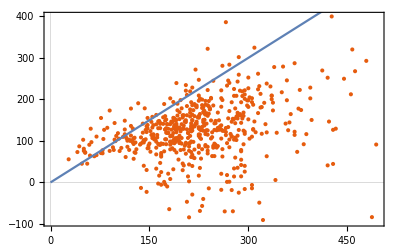

EYrainbow_rapamycin_1stTry, Null Organelles Excluded:

a[i]: {8.28135,0.614946,0.00167816,1.70492,-0.0811318,1.06387}

b[i,j]: (b$20410[1,1] | -0.0349098 | -1.51607×10^-6 | 0.00321738 | -0.0184725 | -0.0458883
b$20410[2,1] | b$20410[2,2] | -9.51933×10^-8 | 0.00133641 | 0.000409029 | -0.0125984
b$20410[3,1] | b$20410[3,2] | b$20410[3,3] | -9.55391×10^-7 | 7.02246×10^-7 | -4.09429×10^-6
b$20410[4,1] | b$20410[4,2] | b$20410[4,3] | b$20410[4,4] | -0.00394728 | -0.0450096
b$20410[5,1] | b$20410[5,2] | b$20410[5,3] | b$20410[5,4] | b$20410[5,5] | 0.00895891
b$20410[6,1] | b$20410[6,2] | b$20410[6,3] | b$20410[6,4] | b$20410[6,5] | b$20410[6,6])

c: 70.7369

alpha[i]: {0.42106,1.36567,2.92489,-0.347826,1.95343,0.186102}

Adjusted R Square: 0.956914

p-values for parameter z-statistics: {0.000173804,0.0600371,0.414056,0.0160399,0.277903,0.153807,0.0920468,0.961171,0.969692,0.22449,0.657287,0.854205,0.632694,0.332812,0.0954971,0.920297,0.648063,0.750655,0.290181,0.205742,0.222141,1.38788×10^-17,0.000566683,1.36862×10^-22,5.53591×10^-16,0.132589,1.77222×10^-10,0.273493}

t-statistics for parameter estimates: {3.77284,1.8833,0.81722,2.41334,-1.08581,1.42762,-1.6868,-0.0486996,0.0380069,-1.21565,-0.443834,-0.183818,0.478129,0.969076,-1.66914,-0.100092,0.456634,-0.31789,-1.05845,-1.26643,1.22184,8.74535,3.46157,10.0959,8.27773,-1.50557,6.46739,1.09584}

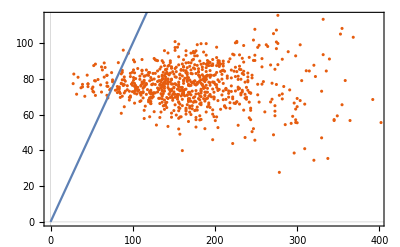

EYrainbow_rapamycin_CheckBistability, Null Organelles Excluded:

a[i]: {0.325983,0.785927,0.0122304,5.97288,1.75468,-0.00410787}

b[i,j]: (b$20548[1,1] | -0.0097669 | -0.0000620316 | -0.341833 | 0.188242 | 0.00137667
b$20548[2,1] | b$20548[2,2] | -8.07812×10^-6 | 0.00383502 | -0.0108679 | -0.000119375
b$20548[3,1] | b$20548[3,2] | b$20548[3,3] | 0.000198508 | -0.000101644 | 2.14408×10^-6
b$20548[4,1] | b$20548[4,2] | b$20548[4,3] | b$20548[4,4] | -0.170171 | -0.00797156
b$20548[5,1] | b$20548[5,2] | b$20548[5,3] | b$20548[5,4] | b$20548[5,5] | 0.00125782
b$20548[6,1] | b$20548[6,2] | b$20548[6,3] | b$20548[6,4] | b$20548[6,5] | b$20548[6,6])

c: 32.5514

alpha[i]: {1.0461,1.29376,2.53252,0.34711,0.704197,-2.01266}

Adjusted R Square: 0.981487

p-values for parameter z-statistics: {0.658657,0.00163728,0.0260901,0.00264742,4.22017×10^-6,0.727303,0.023179,0.0990296,0.00271836,5.98082×10^-6,0.329244,0.0711799,0.548815,0.0174701,0.297429,0.184279,0.0465658,0.317276,0.0654213,0.216901,0.276624,1.84393×10^-9,6.40148×10^-48,1.25456×10^-49,2.1414×10^-85,0.0455774,5.84722×10^-130,6.89254×10^-8}

t-statistics for parameter estimates: {0.44184,3.15392,2.22669,3.01012,4.61431,-0.348769,-2.2724,-1.65042,-3.00204,4.5405,0.9759,-1.80539,0.599648,-2.37884,-1.04226,1.3282,-1.99159,1.00035,-1.84348,-1.23524,1.08826,6.04185,14.9798,15.2713,20.6674,2.00066,26.3629,-5.41638}

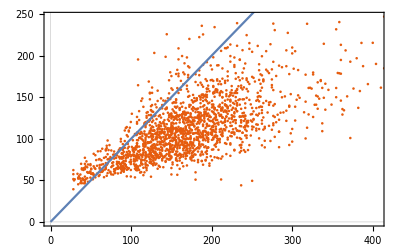

EYrainbow_1nmpp1_1st, Null Organelles Excluded:

a[i]: {3.23557,0.849113,0.118385,1.858,5.40375,0.939394}

b[i,j]: (b$20686[1,1] | -0.0160349 | -0.000552406 | 0.0710163 | -0.236897 | 0.0456767
b$20686[2,1] | b$20686[2,2] | -0.000021895 | 0.00870731 | -0.0248736 | -0.00218286
b$20686[3,1] | b$20686[3,2] | b$20686[3,3] | -0.0017205 | 0.00553555 | -0.0013083
b$20686[4,1] | b$20686[4,2] | b$20686[4,3] | b$20686[4,4] | -0.53927 | 0.194084
b$20686[5,1] | b$20686[5,2] | b$20686[5,3] | b$20686[5,4] | b$20686[5,5] | -0.0965666
b$20686[6,1] | b$20686[6,2] | b$20686[6,3] | b$20686[6,4] | b$20686[6,5] | b$20686[6,6])

c: 18.9915

alpha[i]: {1.16461,1.28294,1.89421,0.321299,0.176525,-0.338914}

Adjusted R Square: 0.972959

p-values for parameter z-statistics: {0.0349517,0.00752647,0.01786,0.222173,6.99877×10^-8,0.0235076,0.0544702,0.526807,0.669128,0.133794,0.365929,0.61408,0.340337,0.0439857,0.345563,0.0945998,0.0954353,0.0620977,0.0049636,0.0125905,0.0537362,0.020628,3.01854×10^-10,2.6837×10^-37,5.62288×10^-52,0.0406864,0.0297826,0.0119854}

t-statistics for parameter estimates: {2.11147,2.67744,2.37198,1.22145,5.42733,2.26816,-1.92508,-0.633083,0.427457,-1.50039,0.90449,-0.504398,0.953903,-2.01649,-0.943625,-1.67302,1.6688,-1.86745,-2.81493,2.49915,-1.93098,2.31799,6.35502,13.2396,15.981,2.04907,2.17573,-2.51665}

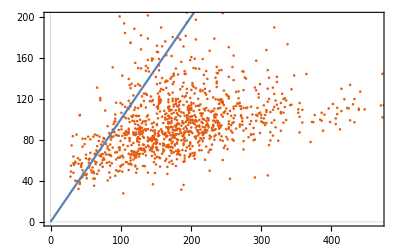

EYrainbow_leucine_large, Null Organelles Excluded:

a[i]: {0.777192,0.0318817,0.226725,0.607523,-1.00337,0.31197}

b[i,j]: (b$20824[1,1] | 0.000127634 | -0.00117717 | 0.0219051 | 0.0171654 | -0.0314166
b$20824[2,1] | b$20824[2,2] | 5.57288×10^-6 | 0.000196753 | -0.00137449 | 0.000432415
b$20824[3,1] | b$20824[3,2] | b$20824[3,3] | -0.000655504 | 0.00202136 | -0.00189286
b$20824[4,1] | b$20824[4,2] | b$20824[4,3] | b$20824[4,4] | -0.0636071 | 0.0520663
b$20824[5,1] | b$20824[5,2] | b$20824[5,3] | b$20824[5,4] | b$20824[5,5] | 0.0394507
b$20824[6,1] | b$20824[6,2] | b$20824[6,3] | b$20824[6,4] | b$20824[6,5] | b$20824[6,6])

c: 44.3594

alpha[i]: {1.60417,1.85493,1.77053,-0.932996,0.715618,-0.102071}

Adjusted R Square: 0.982471

p-values for parameter z-statistics: {0.232151,0.398139,0.0959875,0.121334,0.157551,0.483994,0.660932,0.217989,0.390707,0.717944,0.351782,0.552662,0.503447,0.435585,0.47282,0.20719,0.270336,0.204056,0.0499161,0.0219462,0.00725163,6.8126×10^-8,0.000648626,2.41464×10^-11,2.98783×10^-28,6.69594×10^-9,2.51633×10^-23,0.535732}

t-statistics for parameter estimates: {1.19571,0.845385,1.66652,1.55078,-1.41463,0.700207,0.438784,-1.23283,0.858784,0.361331,-0.931662,0.594018,0.669367,-0.780048,0.718226,-1.26231,1.10303,-1.27108,-1.96354,2.29561,2.69171,5.44532,3.42343,6.77117,11.4412,-5.85932,10.2573,-0.619538}

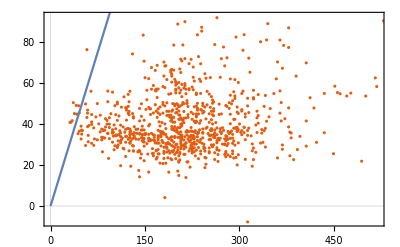

EYrainbowWhi5Up_betaEstrodiol, Null Organelles Excluded:

a[i]: {2.40433,0.9224,0.0576991,0.476838,6.38869,-0.856003}

b[i,j]: (b$20962[1,1] | -0.00383034 | -0.00100755 | -0.0262965 | 0.331118 | -0.461807
b$20962[2,1] | b$20962[2,2] | -0.0000170171 | 0.000825206 | -0.0142203 | 0.0126447
b$20962[3,1] | b$20962[3,2] | b$20962[3,3] | 0.0000933878 | -0.00163663 | 0.00530803
b$20962[4,1] | b$20962[4,2] | b$20962[4,3] | b$20962[4,4] | 0.00936231 | -0.0761732
b$20962[5,1] | b$20962[5,2] | b$20962[5,3] | b$20962[5,4] | b$20962[5,5] | -0.148977
b$20962[6,1] | b$20962[6,2] | b$20962[6,3] | b$20962[6,4] | b$20962[6,5] | b$20962[6,6])

c: -16.2983

alpha[i]: {1.24274,1.16573,2.01106,-1.31614,0.739185,1.51277}

Adjusted R Square: 0.98048

p-values for parameter z-statistics: {0.12729,0.000488108,0.407584,0.178052,0.00002749,0.801776,0.0445394,0.512616,0.196854,0.00445551,0.00646288,0.603328,0.304177,0.0107285,0.110147,0.604034,0.405534,0.485661,0.618303,0.102119,0.501786,0.31834,1.04314×10^-32,1.48718×10^-67,2.4175×10^-9,0.0000124992,4.82192×10^-127,1.06297×10^-7}

t-statistics for parameter estimates: {1.52711,3.50747,0.828767,1.34845,4.22781,-0.251166,-2.01343,-0.655181,-1.29208,2.85537,-2.73343,-0.519911,1.02845,-2.55986,1.60003,0.518898,-0.832398,0.697683,0.49853,-1.63731,-0.672111,-0.99875,12.6991,19.9537,6.06424,-4.40755,31.5452,5.38471}

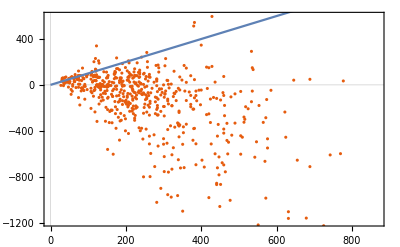

```mathematica
Do[
Print[experiments[[i]],", Null Organelles Excluded:"];
fitCellSizeFromOrganelles[Select[washed,#[[1]]==experiments[[i]]&]];,
{i,1,Length[experiments]}
]
```